## Opakování

1.)

Vytvořte funkci pro převod zadaného libovolného textu na velké písmena a odstraňte z textu diaktritiku.

## Obsah hodiny

IF

Základní řídící (rozhodovací) funkce pro větvení programu nebo algoritmu.
Větví na dvě možnosti podle testovací podmínky

```mathematica
If[True(* nebo False *),
"Pravda",
"Nepravda"
]
```

Pravda

```mathematica
cislo=0;(* pokud zadáme něco jiného tak vrací druhou možnost *)
If[cislo==0,
(* TRUE *)"cislo je 0",
(* FALSE *)"cislo neni 0"
]
```

cislo je 0

Velice často používáme různé relační operátory
	<	menší než
	>	větší než
	<=	menší nebo rovno než
	>=	větší nebo rovno než
	==	rovno
	!=	nerovno
	
Tyto operátory vrací vždy logickou hodnotu True|False.

```mathematica
If[15≥(*>=*)0,
"Ok",
"No"
]
```

Ok

```mathematica
x=10;
If[x==10,"deset"]
```

deset

```mathematica
x++;
If[x≠10,"není deset"]
```

není deset

V části, kde se větví If[] můžeme napsat i více příkazů za sebou, ty ale musí být odděleny od sebe pomocí “;”

```mathematica
x=11;
If[x≥10,
Print["je vetsi jak 10"];
x="A";
Print[x];,(*obycejna carka oddeluje cas TRUE od FALSE*)
Print[x]
]
```

je vetsi jak 10

A

Jednotlivé relační či rozhodovací podmínky můžeme spojovat pomocí logických operátorů:
	&&	AND[]		a zároveň
	||	OR[]		nebo
	!	Not[]		negace

```mathematica
x=5;
y=True;
If[x≥5&&y==True,
"Ok",
"No"
]
```

Ok

Existuje i početná množina funkcí v Mathematice, které umožňují testovat různé vlastnosti a vrací standartně honoty True nebo False

```mathematica
If[StringQ@"toto je text",
"jedná se o text",
"nejedná se o text"
]
```

jedná se o text

Typicky by se mohlo jednat o kontrolu vstupu do nějaké funkce.

```mathematica
(*Caesarova sifra*)
fnc[in_]:=Module[{},
If[!StringQ@in,Return@"Nevložil jste text"];
FromCharacterCode[Mod[ToCharacterCode@ToUpperCase@RemoveDiacritics@in+3,First@ToCharacterCode@"Z"]]
]
fnc@"ahoj"(*provede kód*)
fnc@124 (*zahlásí chybu*)
```

DKRM

Nevložil jste text

Switch

Funkce Switch[] se velmi podobá předchozí funkci If[].
Rozdílem je to, že umužňuje porovnávat více více možností.

```mathematica
x="B";
Switch[
x,
"A","a",
"B","b",
"C","c",
"D","d",
_,"netusim"
]
```

b

Do

První z cyklů: Do[].
Jednoduchý cyklus, který se provádí po určitý počet zadaných iterací.

```mathematica
Do[Print@i,{i,4}]
```

1

2

3

4

Pozn.: nemá výstup.

```mathematica
Do[i,{i,4}]
```

```mathematica
Table[i,{i,4}]
```

{1,2,3,4}

Počet iterací můžeme upravovat podobně jako u funkce Table[].

```mathematica
Do[Print@i,{i,-1,1,0.5}]
```

-1.

-0.5

0.

0.5

1.

Výhoda oproti funkci Table[] je zřejmá, kdy nepotřebujeme výstup v každém kroku; např. při výpisu prvočísel

```mathematica
Table[If[PrimeQ@i,i],{i,1,50}]
```

{Null,2,3,Null,5,Null,7,Null,Null,Null,11,Null,13,Null,Null,Null,17,Null,19,Null,Null,Null,23,Null,Null,Null,Null,Null,29,Null,31,Null,Null,Null,Null,Null,37,Null,Null,Null,41,Null,43,Null,Null,Null,47,Null,Null,Null}

```mathematica
v={};
Do[If[PrimeQ@i,AppendTo[v,i]],{i,1,50}];
v
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}

While

Cyklus podobný předchozímu Do[].
Podmínka se kontroluje na začátku.
Pokud je splněna tak se provede příkaz nebo série příkazů oddělených “;”

```mathematica
a=1;
While[a<5,Print@a;a++];
```

1

2

3

4

```mathematica
(* Výpočet faktoriálu pomocí funkce While[] *)
vstup=5;
vysledek=1;
While[vstup≥1,vysledek*=vstup;vstup--];
vysledek
```

120

For

U tohoto cyklu (příkazu) nastavujeme začátek, konec a velikost kroku po kterou se provádí příkaz.

```mathematica
For[i=0,i≤5,i+=2,Print@i]
```

0

2

4

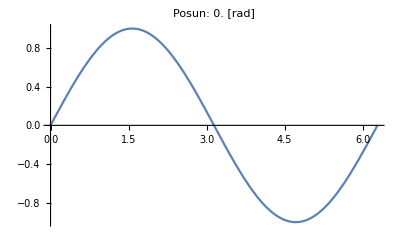

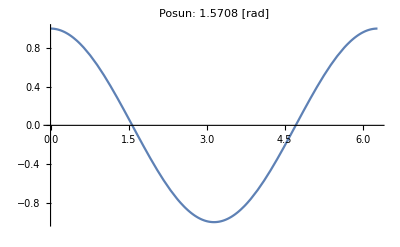

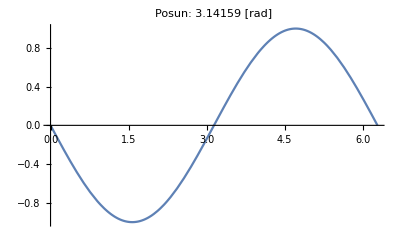

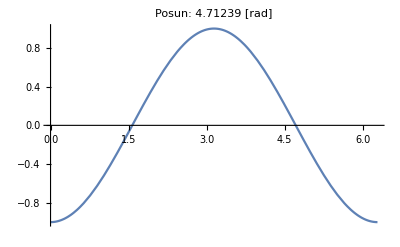

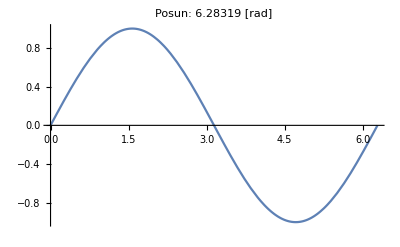

```mathematica
(* Vytvoření skupiny grafů, každý s jiným fázovým posunem *)
For[p=0,p≤2π,p+=π/2,
Print@Plot[Sin[x+p],{x,0,2π},PlotLabel->"Posun: "<>ToString@N@p<>" [rad]"];
];
```

## Samostatný úkol

1.)

Vytvořte funkci pro výpočet kořenů kv. rovnice se zobrazením grafu

2.)

Vytvořte funkci pro převod čísla na text (např 123 -> “jedna dva tři”)

3.)

Vytvořte funkci pro převod čísla o dekadickém základu na dvojkový